```mathematica
SetDirectory["~/mthesis/graphanalysis"]
data=Import["growth-data-filtered"];
T=2000+#[[1]]/12&/@data;
pkgs=#[[2]]&/@data;
newpkgs=#[[3]]&/@data;
delpkgs=#[[4]]&/@data;
deps=#[[5]]&/@data;
rev=#[[6]]&/@data;
```

```mathematica
P[l_]:=Inner[List,T,l,List][[8;;128]];
```

```mathematica
PlotData[l_, opts:OptionsPattern[]]:=
ListLinePlot[P[l],
Filling->{1->0},
PlotStyle->Thickness[.003],
GridLines->{Automatic,None},
AxesOrigin->{2000,0},
FilterRules[{opts},Options[Plot]]
]
```

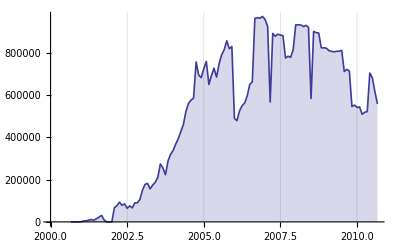

```mathematica
PlotData[deps]
```

```mathematica
Export["depsFiltered.pdf",%,ImageSize->300]
```

depsFiltered.pdf

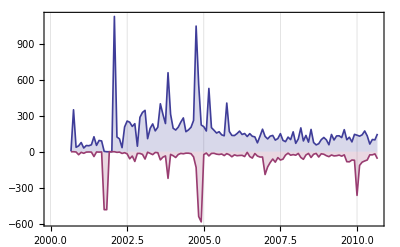

```mathematica
ListLinePlot[{P[newpkgs],P[-delpkgs]},
Filling->{1->0,2->0},
PlotStyle->Thickness[0.003],
GridLines->{Automatic,None},
AxesOrigin->{2000,-00},
PlotStyle->Thick,PlotRange->Full,Frame->True,FrameStyle->{{Black,White},{Black,White}},PlotRange->{{2000,2010.8},{-600,1200}},PlotRangeClipping->True]
```

```mathematica
Export["packageCountDeltaFiltered.pdf",%,ImageSize->300]
```

packageCountDeltaFiltered.pdf

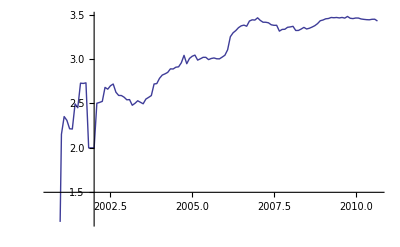

```mathematica
ListPlot[P[deps/pkgs],Joined->True]
```